```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
plot2Doption=Append[{PlotRange->All,PlotStyle->Red,Filling->Axis,GridLines->All,Joined->False},plot2Doption];
```

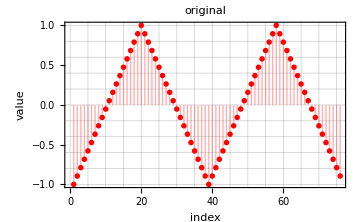

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_original_triangleWave.png

```mathematica
casename="mathematica";

(*cosWave*)
If[casename=="mathematica",
list={1.,1.,2.,2.,1.,1.,0.,0.};
]

n=20;
(*cosWave*)
If[casename=="cosWave",
list=Table[Cos[2π/n*i],{i,0,n-1,1}];
]

(*squareWave*)
If[casename=="squareWave",
list=Flatten[Table[{Table[-1,{i,1,n/2,1}],Table[1,{i,1,n/2,1}]},{i,1,2}]];
]

(*triangleWave*)
If[casename=="triangleWave",
halfWave=Join[Table[i,{i,-1,1,2/(n-1)}],Table[i,{i,1,-1,-2/(n-1)}][[2;;-2]]];
list=Flatten[{halfWave,halfWave}];
]

(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
fig=ListPlot[list,PlotLabel->"original",FrameLabel->{"index","value"},GridLines->All, Joined->False,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_original_"<>casename<>".png"}],fig]
```

```mathematica
num=30
(*list=Flatten@{Table[1,{i,1,num}],Table[2,{i,1,num}]}*)
(*list=Table[Cos[2π*i/num],{i,0,num-1}]*)
MyFourier[list_,n_]:=With[{len=Length[list]},Sum[list[[k+1]]*Exp[-I*n*2. π/len*k],{k,0,len-1}]/len];
Column[Fourier[list,FourierParameters->{-1,-1}],Frame->All]
Column[cn=Table[MyFourier[list,n],{n,0,Length[list]-1}],Frame->All]
```

30

0.
0.
-0.406209
0.
0.
0.
-0.0459665
0.
0.
0.
-0.0171672
0.
0.
0.
-0.00925978
0.
0.
0.
-0.00603885
0.
0.
0.
-0.0044482
0.
0.
0.
-0.00358135
0.
0.
0.
-0.00309655
0.
0.
0.
-0.00284722
0.
0.
0.
-0.00277008
0.
0.
0.
-0.00284722
0.
0.
0.
-0.00309655
0.
0.
0.
-0.00358135
0.
0.
0.
-0.0044482
0.
0.
0.
-0.00603885
0.
0.
0.
-0.00925978
0.
0.
0.
-0.0171672
0.
0.
0.
-0.0459665
0.
0.
0.
-0.406209
0.

2.19123×10^-17
-5.25895×10^-17-2.61122×10^-17 ⅈ
-0.406209-2.10723×10^-16 ⅈ
1.27091×10^-16+2.48339×10^-17 ⅈ
9.05708×10^-17-5.84328×10^-18 ⅈ
3.50597×10^-17+1.11753×10^-16 ⅈ
-0.0459665-1.2417×10^-17 ⅈ
5.84328×10^-17+1.31474×10^-17 ⅈ
9.20316×10^-17+4.82071×10^-17 ⅈ
3.94421×10^-17+4.38246×10^-17 ⅈ
-0.0171672+4.38246×10^-18 ⅈ
-1.46082×10^-18-2.62948×10^-17 ⅈ
2.42496×10^-16+2.77556×10^-17 ⅈ
6.57369×10^-17-4.0903×10^-17 ⅈ
-0.00925978+5.84328×10^-18 ⅈ
-1.01527×10^-16-2.48339×10^-16 ⅈ
6.86585×10^-17-2.498×10^-16 ⅈ
7.99799×10^-17+1.98671×10^-16 ⅈ
-0.00603885+2.62948×10^-17 ⅈ
3.2615×10^-17-2.92164×10^-18 ⅈ
-1.38778×10^-17+3.54979×10^-16 ⅈ
-5.8798×10^-17+2.92164×10^-18 ⅈ
-0.0044482+4.4555×10^-16 ⅈ
3.72509×10^-17+5.25895×10^-17 ⅈ
2.22775×10^-16-5.98936×10^-17 ⅈ
7.40636×10^-16-8.32667×10^-17 ⅈ
-0.00358135+2.46879×10^-16 ⅈ
3.7397×10^-16-1.21248×10^-16 ⅈ
2.86321×10^-16-3.71048×10^-16 ⅈ
-1.18326×10^-16+2.92164×10^-17 ⅈ
-0.00309655+3.52058×10^-16 ⅈ
4.67462×10^-17+4.59428×10^-16 ⅈ
1.28552×10^-16+2.58565×10^-16 ⅈ
9.93357×10^-16-1.2417×10^-17 ⅈ
-0.00284722+3.11885×10^-16 ⅈ
-9.78749×10^-17-3.81639×10^-16 ⅈ
9.20316×10^-17+3.98073×10^-16 ⅈ
3.2138×10^-16+6.53717×10^-17 ⅈ
-0.00277008+2.57469×10^-16 ⅈ
-4.23638×10^-17+2.25879×10^-16 ⅈ
-7.3041×10^-17+4.13777×10^-16 ⅈ
-4.86453×10^-16+7.35888×10^-16 ⅈ
-0.00284722+5.77024×10^-16 ⅈ
-4.55776×10^-16-4.87183×10^-16 ⅈ
6.79281×10^-16-4.12682×10^-16 ⅈ
6.80742×10^-16+3.7397×10^-16 ⅈ
-0.00309655+3.18459×10^-16 ⅈ
-4.35324×10^-16+8.03451×10^-17 ⅈ
-1.66533×10^-16+6.86585×10^-17 ⅈ
-8.38511×10^-16-1.27091×10^-16 ⅈ
-0.00358135+1.36002×10^-15 ⅈ
-1.51195×10^-15+1.03134×10^-15 ⅈ
4.88644×10^-16+9.07169×10^-16 ⅈ
2.33001×10^-16+1.73838×10^-16 ⅈ
-0.0044482+8.5458×10^-16 ⅈ
9.0936×10^-17+6.2377×10^-16 ⅈ
-2.74999×10^-16+2.08897×10^-16 ⅈ
-4.29451×10^-16-9.11552×10^-16 ⅈ
-0.00603885+1.54847×10^-16 ⅈ
-1.22563×10^-15-2.498×10^-16 ⅈ
-8.8197×10^-16-6.07701×10^-16 ⅈ
4.9887×10^-16-2.51261×10^-16 ⅈ
-0.00925978+5.53651×10^-16 ⅈ
-7.63278×10^-16-6.42761×10^-16 ⅈ
-7.07037×10^-16+2.52722×10^-16 ⅈ
-2.77556×10^-16+3.15537×10^-16 ⅈ
-0.0171672-8.76492×10^-18 ⅈ
-5.77024×10^-16+5.93093×10^-16 ⅈ
-2.3081×10^-16+1.76467×10^-15 ⅈ
-1.73838×10^-15+4.6381×10^-16 ⅈ
-0.0459665-5.21513×10^-16 ⅈ
-5.02522×10^-16-4.82801×10^-16 ⅈ
-2.03492×10^-15+7.8446×10^-16 ⅈ
-2.8486×10^-15+7.87017×10^-16 ⅈ
-0.406209-5.65885×10^-15 ⅈ
2.19561×10^-15-1.06695×10^-15 ⅈ

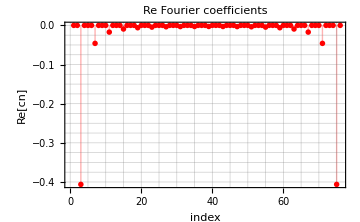

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_cn_triangleWave.png

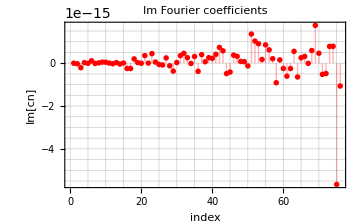

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Im_cn_triangleWave.png

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_ReIm_cn_triangleWave.png

```mathematica
figRe=ListPlot[Re[cn],PlotLabel->"Re Fourier coefficients",FrameLabel->{"index","Re[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_cn_"<>casename<>".png"}],figRe]

figIm=ListPlot[Im[cn],PlotLabel->"Im Fourier coefficients",FrameLabel->{"index","Im[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Im_cn_"<>casename<>".png"}],figIm]

Export[FileNameJoin[{NotebookDirectory[],"./sample_ReIm_cn_"<>casename<>".png"}],Row[{figRe,figIm}]]
```

-1.+4.08135×10^-15 ⅈ
-0.894737+3.16165×10^-15 ⅈ
-0.789474+5.83221×10^-16 ⅈ
-0.684211+5.40642×10^-15 ⅈ
-0.578947-9.78999×10^-17 ⅈ
-0.473684-9.11642×10^-15 ⅈ
-0.368421-1.01204×10^-15 ⅈ
-0.263158+4.21578×10^-15 ⅈ
-0.157895-6.92247×10^-15 ⅈ
-0.0526316+3.23083×10^-15 ⅈ
0.0526316+2.36315×10^-15 ⅈ
0.157895-5.96321×10^-15 ⅈ
0.263158-1.09123×10^-15 ⅈ
0.368421-5.86392×10^-15 ⅈ
0.473684-3.09118×10^-15 ⅈ
0.578947+4.24576×10^-15 ⅈ
0.684211-4.18961×10^-15 ⅈ
0.789474-4.7418×10^-16 ⅈ
0.894737+2.98012×10^-15 ⅈ
1.+4.35446×10^-15 ⅈ
0.894737+2.2322×10^-15 ⅈ
0.789474+4.25204×10^-15 ⅈ
0.684211+1.79294×10^-15 ⅈ
0.578947-2.22721×10^-15 ⅈ
0.473684+2.03581×10^-15 ⅈ
0.368421+7.02183×10^-15 ⅈ
0.263158+5.06028×10^-15 ⅈ
0.157895+1.31031×10^-15 ⅈ
0.0526316+2.478×10^-15 ⅈ
-0.0526316-4.12855×10^-17 ⅈ
-0.157895-6.46417×10^-15 ⅈ
-0.263158-9.86626×10^-16 ⅈ
-0.368421-1.10682×10^-15 ⅈ
-0.473684-5.23077×10^-15 ⅈ
-0.578947-3.6424×10^-15 ⅈ
-0.684211-3.28367×10^-15 ⅈ
-0.789474-1.05927×10^-14 ⅈ
-0.894737-3.35804×10^-15 ⅈ
-1.+1.60958×10^-15 ⅈ
-0.894737-8.76157×10^-15 ⅈ
-0.789474-2.30878×10^-15 ⅈ
-0.684211-6.04393×10^-15 ⅈ
-0.578947-2.40467×10^-15 ⅈ
-0.473684-4.59807×10^-15 ⅈ
-0.368421-1.86884×10^-15 ⅈ
-0.263158-1.61308×10^-15 ⅈ
-0.157895+3.03987×10^-15 ⅈ
-0.0526316+9.94867×10^-16 ⅈ
0.0526316-4.01085×10^-15 ⅈ
0.157895+1.0043×10^-14 ⅈ
0.263158+3.96574×10^-15 ⅈ
0.368421-1.96932×10^-15 ⅈ
0.473684+1.03963×10^-15 ⅈ
0.578947+8.31709×10^-15 ⅈ
0.684211+1.3998×10^-14 ⅈ
0.789474+1.48317×10^-14 ⅈ
0.894737+1.59335×10^-14 ⅈ
1.+5.11512×10^-15 ⅈ
0.894737+1.92632×10^-14 ⅈ
0.789474+1.48155×10^-14 ⅈ
0.684211+3.51961×10^-15 ⅈ
0.578947+6.43447×10^-15 ⅈ
0.473684-1.08222×10^-15 ⅈ
0.368421+4.98312×10^-15 ⅈ
0.263158+1.57216×10^-15 ⅈ
0.157895+4.86548×10^-15 ⅈ
0.0526316+3.18352×10^-16 ⅈ
-0.0526316-4.36906×10^-15 ⅈ
-0.157895+2.15437×10^-15 ⅈ
-0.263158-5.55562×10^-15 ⅈ
-0.368421-4.21305×10^-15 ⅈ
-0.473684-1.52442×10^-14 ⅈ
-0.578947-1.53405×10^-14 ⅈ
-0.684211-1.12569×10^-14 ⅈ
-0.789474-1.07978×10^-14 ⅈ
-0.894737-2.14261×10^-14 ⅈ

-1.+4.08135×10^-15 ⅈ
-0.894737+3.09913×10^-15 ⅈ
-0.789474+6.12377×10^-16 ⅈ
-0.684211+5.42112×10^-15 ⅈ
-0.578947-1.12227×10^-16 ⅈ
-0.473684-8.90896×10^-15 ⅈ
-0.368421-1.2617×10^-15 ⅈ
-0.263158+4.06764×10^-15 ⅈ
-0.157895-7.07552×10^-15 ⅈ
-0.0526316+3.3346×10^-15 ⅈ
0.0526316+2.32495×10^-15 ⅈ
0.157895-6.10723×10^-15 ⅈ
0.263158-8.11834×10^-16 ⅈ
0.368421-5.76946×10^-15 ⅈ
0.473684-3.32745×10^-15 ⅈ
0.578947+4.04396×10^-15 ⅈ
0.684211-4.22221×10^-15 ⅈ
0.789474-4.53901×10^-16 ⅈ
0.894737+2.98346×10^-15 ⅈ
1.+4.31591×10^-15 ⅈ
0.894737+2.17435×10^-15 ⅈ
0.789474+4.25495×10^-15 ⅈ
0.684211+1.76947×10^-15 ⅈ
0.578947-2.14654×10^-15 ⅈ
0.473684+2.19266×10^-15 ⅈ
0.368421+6.95901×10^-15 ⅈ
0.263158+4.8517×10^-15 ⅈ
0.157895+1.30966×10^-15 ⅈ
0.0526316+2.60446×10^-15 ⅈ
-0.0526316-9.14471×10^-17 ⅈ
-0.157895-6.50181×10^-15 ⅈ
-0.263158-1.08483×10^-15 ⅈ
-0.368421-1.10585×10^-15 ⅈ
-0.473684-5.51151×10^-15 ⅈ
-0.578947-3.61731×10^-15 ⅈ
-0.684211-3.14067×10^-15 ⅈ
-0.789474-1.05778×10^-14 ⅈ
-0.894737-3.3091×10^-15 ⅈ
-1.+1.59394×10^-15 ⅈ
-0.894737-8.78903×10^-15 ⅈ
-0.789474-2.38873×10^-15 ⅈ
-0.684211-5.97623×10^-15 ⅈ
-0.578947-2.38577×10^-15 ⅈ
-0.473684-4.74678×10^-15 ⅈ
-0.368421-1.7359×10^-15 ⅈ
-0.263158-1.51413×10^-15 ⅈ
-0.157895+3.18974×10^-15 ⅈ
-0.0526316+8.84247×10^-16 ⅈ
0.0526316-3.99028×10^-15 ⅈ
0.157895+1.0104×10^-14 ⅈ
0.263158+3.92046×10^-15 ⅈ
0.368421-2.11312×10^-15 ⅈ
0.473684+9.9598×10^-16 ⅈ
0.578947+8.27951×10^-15 ⅈ
0.684211+1.40477×10^-14 ⅈ
0.789474+1.47758×10^-14 ⅈ
0.894737+1.59181×10^-14 ⅈ
1.+5.13267×10^-15 ⅈ
0.894737+1.92807×10^-14 ⅈ
0.789474+1.48409×10^-14 ⅈ
0.684211+3.44857×10^-15 ⅈ
0.578947+6.36539×10^-15 ⅈ
0.473684-1.08244×10^-15 ⅈ
0.368421+4.92038×10^-15 ⅈ
0.263158+1.5876×10^-15 ⅈ
0.157895+4.68554×10^-15 ⅈ
0.0526316+6.0074×10^-17 ⅈ
-0.0526316-4.46047×10^-15 ⅈ
-0.157895+1.94989×10^-15 ⅈ
-0.263158-5.57651×10^-15 ⅈ
-0.368421-4.33425×10^-15 ⅈ
-0.473684-1.52497×10^-14 ⅈ
-0.578947-1.5201×10^-14 ⅈ
-0.684211-1.12367×10^-14 ⅈ
-0.789474-1.09051×10^-14 ⅈ
-0.894737-2.13934×10^-14 ⅈ

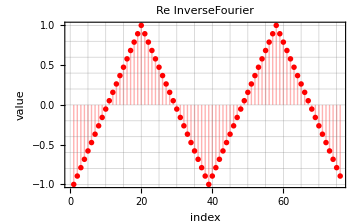

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_inv_triangleWave.png

```mathematica
len=Length[list];
MyInverseFourier[list_,n_,max_ :(len-1)]:=With[{len=Length[list]},Sum[list[[k+1]]*Exp[I*n*2 π/len*k],{k,0,max}]/len];
Column[inv=InverseFourier[cn,FourierParameters->{-1,-1}],Frame->All]
Column[Table[MyInverseFourier[cn,n]*(Length[list]),{n,0,Length[list]-1,1}],Frame->All]

fig=ListPlot[Re[inv],PlotLabel->"Re InverseFourier",FrameLabel->{"index","value"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_inv_"<>casename<>".png"}],fig]
```

```mathematica
(*n-1->-1*)
(*n-2->-2*)
Floor[Length[cn]-1]
shift=If[EvenQ[(Length[cn]-1)/2],{(Length[cn]-1)/2,(Length[cn]-1)/2},{(Length[cn]-1+1)/2,(Length[cn]-1-1)/2}]
Do[Cn[i]=cn[[i+1]],{i,0,shift[[1]]}]
Do[Cn[-i]=cn[[Length[cn]+1-i]],{i,1,shift[[2]]}]
```

75

{38,37}

```mathematica
Column@Table[{i,Re@Cn[i]},{i,-shift[[2]],shift[[1]],1}]
```

{-37,-4.23638×10^-17}
{-36,-7.3041×10^-17}
{-35,-4.86453×10^-16}
{-34,-0.00284722}
{-33,-4.55776×10^-16}
{-32,6.79281×10^-16}
{-31,6.80742×10^-16}
{-30,-0.00309655}
{-29,-4.35324×10^-16}
{-28,-1.66533×10^-16}
{-27,-8.38511×10^-16}
{-26,-0.00358135}
{-25,-1.51195×10^-15}
{-24,4.88644×10^-16}
{-23,2.33001×10^-16}
{-22,-0.0044482}
{-21,9.0936×10^-17}
{-20,-2.74999×10^-16}
{-19,-4.29451×10^-16}
{-18,-0.00603885}
{-17,-1.22563×10^-15}
{-16,-8.8197×10^-16}
{-15,4.9887×10^-16}
{-14,-0.00925978}
{-13,-7.63278×10^-16}
{-12,-7.07037×10^-16}
{-11,-2.77556×10^-16}
{-10,-0.0171672}
{-9,-5.77024×10^-16}
{-8,-2.3081×10^-16}
{-7,-1.73838×10^-15}
{-6,-0.0459665}
{-5,-5.02522×10^-16}
{-4,-2.03492×10^-15}
{-3,-2.8486×10^-15}
{-2,-0.406209}
{-1,2.19561×10^-15}
{0,2.19123×10^-17}
{1,-5.25895×10^-17}
{2,-0.406209}
{3,1.27091×10^-16}
{4,9.05708×10^-17}
{5,3.50597×10^-17}
{6,-0.0459665}
{7,5.84328×10^-17}
{8,9.20316×10^-17}
{9,3.94421×10^-17}
{10,-0.0171672}
{11,-1.46082×10^-18}
{12,2.42496×10^-16}
{13,6.57369×10^-17}
{14,-0.00925978}
{15,-1.01527×10^-16}
{16,6.86585×10^-17}
{17,7.99799×10^-17}
{18,-0.00603885}
{19,3.2615×10^-17}
{20,-1.38778×10^-17}
{21,-5.8798×10^-17}
{22,-0.0044482}
{23,3.72509×10^-17}
{24,2.22775×10^-16}
{25,7.40636×10^-16}
{26,-0.00358135}
{27,3.7397×10^-16}
{28,2.86321×10^-16}
{29,-1.18326×10^-16}
{30,-0.00309655}
{31,4.67462×10^-17}
{32,1.28552×10^-16}
{33,9.93357×10^-16}
{34,-0.00284722}
{35,-9.78749×10^-17}
{36,9.20316×10^-17}
{37,3.2138×10^-16}
{38,-0.00277008}

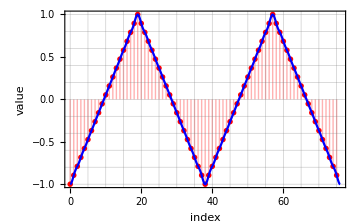

```mathematica
f[t_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-shift[[2]],shift[[1]],1}]];
fig=Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_interpolation_"<>casename<>".png"}],fig]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_interpolation_triangleWave.png

```mathematica
f[t_,expandmax_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-expandmax,expandmax,1}]];
anim=Manipulate[
Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t,expandmax]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
,PlotLabel->expandmax
],{expandmax,1,Min[shift],1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_convergence_"<>casename<>".gif"}],anim]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_convergence_triangleWave.gif